```mathematica
dataGMR = Import["M:\\MR_2020\\MR_distributions\\-300_Oe\\GMR_minus_-300_Oe.scale.txt", "Table"];
dataNMMR = Import["M:\\MR_2020\\MR_distributions\\-300_Oe\\NMMR_minus_300_Oe.scale.txt",  "Table"];
magntop = Import["M:\\MR_2020\\MR_distributions\\-300_Oe\\magn_top_minus_300_Oe.txt", "Table"];
magnbottom = Import["M:\\MR_2020\\MR_distributions\\-300_Oe\\magn_bot_minus_300_Oe.txt", "Table"];
fieldbottom = Import["M:\\MR_2020\\MR_distributions\\-300_Oe\\hext_bot_minus_300_Oe.txt", "Table"];
SetOptions[EvaluationNotebook[],FontSize->16]
```

```mathematica
ListPlot3D[dataNMMR,  PlotRange->All, Mesh->None,  ColorFunction->"TemperatureMap", AxesLabel->{Style["X, nm",Large,Bold,Black],Style["Y, nm",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10,Thick, FontFamily-> "Times New Roman"],  TicksStyle->Directive[Thick, 20]]
```

-Graphics3D-

```mathematica
ListPlot3D[dataGMR,  PlotRange->All, Mesh->None,  ColorFunction->"TemperatureMap", AxesLabel->{Style["X, nm",Large,Bold,Black],Style["Y, nm",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10,Thick, FontFamily-> "Times New Roman"],  TicksStyle->Directive[Thick, 20]]
```

-Graphics3D-

```mathematica
ListPlot3D[magntop,  PlotRange->All, Mesh->None,  ColorFunction->"TemperatureMap", AxesLabel->{Style["X, m",Large,Bold,Black],Style["Y, m",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10, FontFamily-> "Times New Roman"],TicksStyle->20]
```

-Graphics3D-

```mathematica
ListPlot3D[magnbottom,  PlotRange->All, Mesh->None,  ColorFunction->"TemperatureMap", AxesLabel->{Style["X, m",Large,Bold,Black],Style["Y, m",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10, FontFamily-> "Times New Roman"],TicksStyle->20]
```

-Graphics3D-

```mathematica
ListPlot3D[fieldbottom,  PlotRange->All, Mesh->None,  ColorFunction->"TemperatureMap", AxesLabel->{Style["X, m",Large,Bold,Black],Style["Y, m",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10, FontFamily-> "Times New Roman"],TicksStyle->20]
```

-Graphics3D-

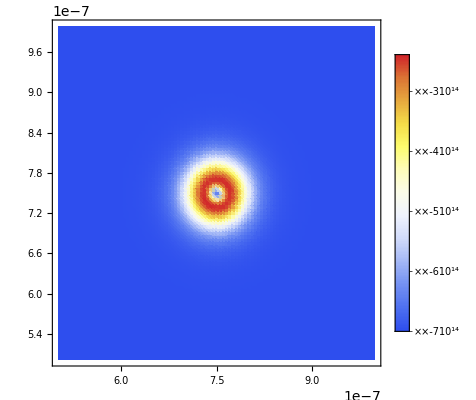

```mathematica
ListDensityPlot[dataNMMR,PlotRange->All,  ColorFunction->"TemperatureMap", PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

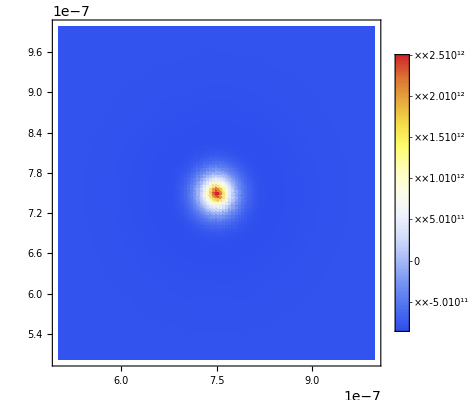

```mathematica
ListDensityPlot[dataGMR,PlotRange->All,  ColorFunction->"TemperatureMap", PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

```mathematica
ListPlot3D[dataNMMR,  PlotRange->All, Mesh->None,  ColorFunction->"GrayTones", AxesLabel->{Style["X, nm",Large,Bold,Black],Style["Y, nm",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10,Thick, FontFamily-> "Times New Roman"],  TicksStyle->Directive[Thick, 20]]
```

-Graphics3D-

```mathematica
ListPlot3D[dataGMR,  PlotRange->All, Mesh->None,  ColorFunction->"GrayTones", AxesLabel->{Style["X, nm",Large,Bold,Black],Style["Y, nm",Large,Bold,Black]},LabelStyle-> Directive[Black, Bold, 20, FontFamily-> "Times New Roman"], PlotLegends->Automatic, AxesStyle->Directive[10,Thick, FontFamily-> "Times New Roman"],  TicksStyle->Directive[Thick, 20]]
```

-Graphics3D-